Computational Journey of Quantum Mechanics | Amir H. Ebrahimnezhad | Advisor: Prf. Ebrahim | University of Tehran

# Symbolic Computation in Scientific Research

## Computational Journey of Quantum Mechanics

## Overview

## What is this notebook about?

We’re using Mathematica as our main tool of discussions. And this tool is different than programming languages and frameworks. Mathematica is a general system for computation, which is opposed to numerical computation libraries and frameworks in come crucial ways (although one can theoretically build one inside each language). In this notebook we’ll explore what are the differences between Mathematica, and General Purpose Languages (such as python and C/C++). We’ll also get to know the basics of symbolic computation in this software and how to use it to compute, manipulate, and visualize simple mathematical expressions.

For people who are already familiar with symbolic computation and Mathematica in specific, there’s no need to look at this notebook. But it might be helpful to skim it once.

## Overview of Mathematica

### What is Mathematica

Mathematica is a general system for computation. The name “Mathematica” may suggest it’s only for math, but this is not the case. The platform began as a system for doing mathematics by computer, but it’s evolved into the Wolfram Language, which can be used for all types of computation.

### First Step

When you first start Mathematica, you begin by creating a Notebook. This is a living computational document and defaults to input/output mode. Mean that you enter a command, and receive and output.

```mathematica
LatticeData["FaceCenteredCubic", "Image"]
```

-Graphics3D-

Let’s begin by doing some simple calculations:

```mathematica
Exp[ⅈ π] + 3! Tan[π/3] + 1/(4!)
```

-23/24+6 √3

There are multiple interesting things here that we’ve to take notice. First, the result is exact. Mathematica does not convert fractions to rounded off decimals. It treats them with infinite precision. Next, functions in Mathematica are capitalized and use square brackets, not parentheses. If you want an approximation, you can ask for it using the N function, by the desired precision:

```mathematica
N[%, 13]
```

9.43397151208

Where % denotes the last output that Mathematica had generated before running this cell.

### Algebra

You can do algebra easily in Mathematica, for example let’s find the solutions to a polynomial of degree . You can use the `Solve` function, enter the equation (notice how we use double equals here) followed by a comma and the name of the variable you’re solving for.

```mathematica
Solve[x^2+2 x+3 ==0, x]
```

{{x→-1-ⅈ √2},{x→-1+ⅈ √2}}

```mathematica
N[%,4]
```

{{x→-1.-1.414 ⅈ},{x→-1.+1.414 ⅈ}}

The output may look different than you expect! this is because Mathematica returns the solutions as a list of substitution rules. You can also solve a general quadratic equation with constants :

```mathematica
Solve[a x^2+b x +c ==0, x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

Notice we didn’t tell anything to Mathematica about the constants. This is one of the potentials of both Mathematica and Symbolic computation in general. Everything is a symbol, and patterns rule.

### Systems of Equations

What about systems of equations? No problem, again, we’ll use the `Solve` function. This time we pass two lists (or one list and a variable to solve for). Lists are ordered-collections of data, we’ll get back to them later:

```mathematica
{a,b,c}
```

{a,b,c}

```mathematica
Solve[{
2 a + 3b - 2c == 0,
a + b==3,
-c -3 a ==5
}, {a,b,c}]
```

{{a→-19/5,b→34/5,c→32/5}}

### Defining a Function

Functions are crucial for mathematics, and Mathematica has an easy way to define them:

```mathematica
F[x_]:= x Sin[1/x]+Cos[x]/(x^2+1)
```

For now don’t worry about the syntax. Now you can pass them values and get the respective output of them:

```mathematica
F[1]
F[π]
F[2+√3] // N
```

Cos[1]/2+Sin[1]

-1/(1+π^2)+π Sin[1/π]

0.932431

The last example uses `// N` which is a short form for writing:

```mathematica
N[F[2+√3]]
```

0.932431

Now let’s plot this function to have a better look:

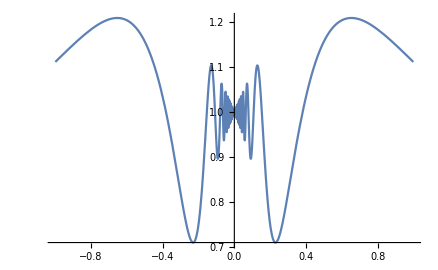

```mathematica
Plot[F[x],{x,-1,1}]
```

We can use `Limit` Function to take the limit. Notice the syntax of mapping `x` to `π/4`.

```mathematica
Limit[F[x],x->π/4]
```

1/(√2 (1+π^2/16))+1/4 π Sin[4/π]

### Differentiation

Differentiation is also not a hard task in Mathematica, the function is so useful that the name is `D` for shortening the writing process:

```mathematica
D[F[x],x]
%//Simplify
%//FullSimplify
```

-Cos[1/x]/x-(2 x Cos[x])/((1+x^2)^2)+Sin[1/x]-Sin[x]/(1+x^2)

-Cos[1/x]/x-(2 x Cos[x])/((1+x^2)^2)+Sin[1/x]-Sin[x]/(1+x^2)

-Cos[1/x]/x+Sin[1/x]-(2 x Cos[x]+(1+x^2) Sin[x])/((1+x^2)^2)

You can use `Simplify` and `FullSimplify` to cancel out terms, re-factoring and overall simplifying the expression that you’re working with. The latter would try harder and might take longer to compute. As you can see above, `Simplify` didn’t do anything but `FullSimplify` found a way around.

For higher order differentiation, use a list of variable and the number of times you want to differentiate with respect to:

```mathematica
D[F[x],{x,4}]
```

Cos[x]/(1+x^2)+((384 x^4)/((1+x^2)^5)-(288 x^2)/((1+x^2)^4)+24/((1+x^2)^3)) Cos[x]-6 ((8 x^2)/((1+x^2)^3)-2/((1+x^2)^2)) Cos[x]+x (-(12 Cos[1/x])/x^7+(24 Cos[1/x])/x^5+Sin[1/x]/x^8-(36 Sin[1/x])/x^6)+4 (Cos[1/x]/x^6-(6 Cos[1/x])/x^4+(6 Sin[1/x])/x^5)-(8 x Sin[x])/((1+x^2)^2)-4 (-(48 x^3)/((1+x^2)^4)+(24 x)/((1+x^2)^3)) Sin[x]

```mathematica
%//FullSimplify
```

-(8 Cos[1/x])/x^6+((37-248 x^2+66 x^4-32 x^6+x^8) Cos[x])/((1+x^2)^5)+((1-12 x^2) Sin[1/x])/x^7-(8 x (13-10 x^2+x^4) Sin[x])/((1+x^2)^4)

### Integration

Speaking of Differentiation might remind you of integration. And of-course Mathematica is able to do that. Use `Integrate` for both Definite and Indefinite integration. Pass the function, and the variable (for indefinite) and a list containing variable, lower bound and upper bound (for definite).

```mathematica
F[x]
```

Cos[x]/(1+x^2)+x Sin[1/x]

```mathematica
Integrate[F[x],{x,-1,3}]//FullSimplify //N
Integrate[F[x],x]//FullSimplify
```

3.95592+4.08428×10^-17 ⅈ

1/(4 ⅇ)(2 ⅇ x Cos[1/x]-ⅈ (1+ⅇ^2) CosIntegral[ⅈ-x]+ⅈ (1+ⅇ^2) CosIntegral[ⅈ+x]+2 ⅇ x^2 Sin[1/x]-SinIntegral[ⅈ-x]+ⅇ^2 SinIntegral[ⅈ-x]+2 ⅇ SinIntegral[1/x]-(-1+ⅇ^2) SinIntegral[ⅈ+x])

## Fundamentals Of Mathematica

We’ve went through some commands in the last section just to get you familiar with the syntax of Mathematica. This section provides a complementary documentation of commands and their output.

## Why Mathematica?

Mathematica is a mathematical software package created by Stephen Wolfram more  than 35 years ago. Its first official version (Mathematica 1.0) emerged in 1988 and  was created as an algebraic computational system capable of handling symbolic  computations. 

However, Mathematica has established itself as a tool capable of  performing complex tasks efficiently, automatically, and intuitively. Mathematica is widely used in many disciplines like engineering, optics, physics, graph theory, financial  engineering, game development, and software development.  Mathematica provides a complete, integrated platform to import, analyze, and  visualize data. 

Mathematica does not require plug-ins. It also has a mixed syntax,  performing both symbolic and numerical calculations. It provides an accessible way  to read the code with the implementation of notebooks as a standard format, which  also serves to create detailed reports of the processes carried out. 

Mathematica can  be characterized as a powerful platform enabling efficient and concise forms of work.  Among computer languages, the Wolfram Language falls into the group of programming  languages classified as a high-level, multi-paradigm interpreted language. Unlike  conventional programming languages, the Wolfram Language adheres to unique rules,  facilitating order and clear, compact code composition.

## The Wolfram Language

Mathematica is powered by the Wolfram Language, an interpreted high-level programming language that covers both symbolic and numeric capabilities. To understand the Wolfram Language, it is necessary to remember that the language’s core nature resembles a normal mathematical text, as opposed to other programming languages’ syntax.

The first letter of a built-in function word is uppercase and is also human-readable.

Any element introduced in the language is taken as an expression.

Expressions take values consisting of the Wolfram Language atomic expressions.

A symbol made up of letter, numbers, or alphanumeric contents.

Four types of numbers, Integers, rational, real, and complex.

The default character string is written with the quotation marks “”.

In Mathematica, there are three ways to group expressions.

Parentheses group terms within and expression.

Command entries are enclosed by brackets. Also, square brackets enclose the arguments of a function.

Mathematica uses curly braces {} to represent lists, arrays, matrices and other collections.

## Structure of Mathematica

The core interaction between the user and Mathematica, happens inside Notebooks. Notebooks can be saved locally from the menu bar by selecting File > Save. Initializing Mathematica always exhibits an untitled notebook. 

Notebooks serve as the standard document format. They can be customized to display text alongside computations. However, the key feature of Mathematica lies in its capacity to perform computations, extending beyond numerical calculations, regardless of the notebook’s purpose.

Mathematica’s notebooks are separated into input spaces called cells. Cells are  represented by the square brackets on the notebook’s right side. Each input and output  cell has its bracket. Brackets enclosed by larger brackets are related computations,  whether input or output. Grouped cells are represented by nested brackets that contain  the whole evaluation cell. Other cells can be grouped by selecting and grouping them  with the right-click option. Cells can also have the capability to show or hide input by  simply double-clicking the cells. To add a new cell, move the text cursor down, and a flat  line should appear, marking the new cell ready to receive input expressions. The plus  tab in the line is the assistant input tab, showing the various types of input supported by  Mathematica.

```mathematica
"Hello World!"
```

Hello World!

## Input Types

There are four main input types. The default input is the Wolfram Language code  input. Free-form input is involved with Wolfram knowledge-base servers, and the results  are shown in Wolfram Language syntax. Wolfram Alpha query is associated with results  explicitly shown on the Wolfram Alpha website. External Language Input is built-in  support for common external programming supported by Mathematica.

### Default input: Wolfram Language Code Input.

```mathematica
Integrate[x,x]
```

x^2/2

### Free-form input: involved with Wolfram knowledge-base servers and the results are shown in Wolfram language syntax

```mathematica
EntityClass["Particle","Boson"][EntityProperty["Particle","Mass"]][[1]] (*So many values I just selected the first one!*)
```

5.27932 GeV/c^2

### External Language Input: built-in support for common external programming supported by Mathematica

print("Hello From Python in Mathematica")

Hello From Python in Mathematica

/usr/local/Wolfram/Mathematica/13.2/SystemFiles/Components/WolframClientForPython/wolframclient/serializers/utils.py:12: SyntaxWarning: invalid escape sequence '\.'

chr(0): "\.00",

## Design of Mathematica

Now that you have the lay of the land of Mathematica' s basic format, you can learn the internal structure of how Mathematica works . Inside Mathematica, there are two fundamental processes: the Mathematica kernel and the graphical interface . 

The Mathematica kernel is the one that takes care of performing the programming computations; it is where the Wolfram Language is interpreted and is associated with each Mathematica session . 

The Mathematica interface allows the user to interact with the Wolfram Language functions and, at the same time, document your progress.

Each notebook contains cells, where the commands that the Mathematica kernel  receives are written and then evaluated. 

Each cell has an associated number. There are  two types of cells: the Input cell and the Output cell. 

These are associated with each other  and have the following expressions: 

In[n]:= Expression 
and 
Out [n]: = Result or (“new  expr”). 

The evaluations are listed according to which cell is evaluated first and continue  in ascending order. When quitting the kernel session, all the information, computations  made, and stored variables are relinquished, and the kernel is restarted, including the  cell expressions.

To start a new kernel session, Click Evaluation > Start Kernel > Local

To quit a kernel session, select Evaluation > Quit Kernel > Local.

Let’s begin:

```mathematica
(11*17) + (4/2)
```

189

The computation shows that In and Out have a number enclosed. This number is the number associated with the evaluated expression.

After running each cell, a suggestion bar appears. The suggestion bar in Mathematica is always visible unless the user hides it. But the suggestion bar offers suggestions for possible new commands or functions to be applied to generate output.

The input form of Mathematica is intuitive; to write in a Mathematica notebook,  you just have to put the cursor in a blank space, and the cursor indicates that you are  inside a cell that has not been evaluated. To evaluate a cell, click the keys [Shift + Enter],  instructing Mathematica kernel to evaluate the expression written. The next chapter  looks at the new form to evaluate expressions using the new toolbar.

## Expressions in Mathematica

Basic arithmetic operations can be performed in Mathematica with a common intuitive form.

```mathematica
(3*3) + (Sin[Pi/2]*1.57734)
```

10.5773

Mathematica also provides the capability to use a traditional mathematical notation.  To insert a placeholder in the form, click [Ctrl + 6]. To indicate the product operation, use  a space between expressions or add an asterisk (*) between.

```mathematica
1.32^23*2
```

1186.4

```mathematica
2 10
```

20

The standard Mathematica format aims to deliver the value closest to its regular  form, so when dealing with decimal numbers or general math notation, Mathematica  always gives you the best precision (involving, in some circumstances, infinite  precision). However, it allows you to manipulate expressions numerically, to display  numeric values, you use the N function. To insert the square root, type [Ctrl + 2].

```mathematica
√2
```

√2

```mathematica
√2//N
```

1.41421

You can manage the number precision of a numeric expression. In this case, you  establish 10 decimal places

```mathematica
N[√2, 10]
```

1.414213562

For a shortcut to work with the decimal point, just type a dot (.) anywhere in the  expression, and with this, you are telling Mathematica to calculate the value with  machine precision.

```mathematica
4/3
```

4/3

```mathematica
{4/3., 4./3., 4./3}
```

{1.33333,1.33333,1.33333}

Mathematica performs the sequence of operations from left to right, in line with the  written expression, while adhering to the standard order of mathematical operations. To  evaluate an expression without showing the result, you add a semicolon (;) after the end  of the first term. In the following example, the 11/7 is evaluated but not shown, and the  other term is displayed.

```mathematica
11/7;
Sqrt[4]
```

2

The last form of code is called a compound expression. Expressions can be written in  a single line of code, and with compound expressions, they are evaluated in the intended  sequence. If you write the semicolon in each expression, Mathematica does not return  the values, but they are evaluated.

### Assigning Values

In the Wolfram Language, each variable requires a unique identifier that distinguishes  it from the others. A variable in the Wolfram Language can be a union of more than one  letter and digits; it must also not coincide with protected words—reserved words that  refer to commands or built-in functions. Keep in mind that the Wolfram Language is  case-sensitive. User variables are advised to be lowercase to avoid confusion with builtin symbols.

```mathematica
r = 10;
a = 2. Pi r^2
```

628.319

To determine whether a word is reserved within the Wolfram Language, use the  Attributes command; this displays the attributes to the associated command. Attributes  are general aspects that define functions in the Wolfram Language. When the word  “Protected” appears in the attributes, it means that the word of the function is reserved.  The next example shows whether the word “Power” is reserved.

```mathematica
Attributes[Power]
```

{Listable,NumericFunction,OneIdentity,Protected,ReadProtected}

As seen in the attributes, “Power” is a protected word. Importantly, most of the builtin functions in Mathematica are listable—that is, the function is interleaved to the lists  that appear as arguments to the function.

Variables can be presented in a notebook in the following ways: (1) global variables,  or those that are defined and can be used throughout the notebook, like the ones in  the earlier examples; and (2) local variables, which are defined in only one block that  corresponds to what is known as a module, in which they are only defined within  a module. A module has the following form: Module [symbol1, symbol 2... body of  module].

```mathematica
Module[{l=1, k=2,h=3}, Sin[l + h +2 k] + k]
l
```

2+Sin[8]

l

Variables can be cleared with multiple commands, but the most suitable command  is the Clear[symbol], which removes assigned values from the specified variable or  variables. So, if you evaluate the variable after Clear, Mathematica treats it as a symbol,  and you can check it with the command Head; Head always gives you the head of the  expression, which is the type of object in the Wolfram Language. And if you check the head a, you see that “a” is a symbol.

```mathematica
a = 10;
Head[a]
```

Integer

```mathematica
Clear[a]
```

```mathematica
Head[a]
```

Symbol

Symbols or variables assigned during a session remain in the memory unless they  are removed or the kernel session ends.

### Built-in Functions

Built-in commands or functions are written in common English with the first letter  capitalized. Some functions have abbreviations, while others employ PascalCase  notation with two capital letters. Here, different examples of functions are presented.  Built-in functions and group expressions often require arguments, which are values that  the function needs to execute the correct operation. Functions may or may not accept  arguments; they are separated by commas.

```mathematica
RandomInteger[{0,33}]
```

20

Some commands or built-in functions in Mathematica have options that can be  specified in a particular expression. To see whether a built-in function has available options, use Option. In the next example, the RandomReal function creates a pseudorandom real number between an established interval.

```mathematica
Options[RandomReal]
```

{WorkingPrecision→MachinePrecision}

RandomReal has only one option for specifying specific instructions within the  WorkingPrecision command. 

The default value for this option is MachinePrecision.  WorkingPrecision defines the number of digits of precision for internal computations,  while MachinePrecision is the symbol used to approximate real numbers, denoted by  $MachinePrecision.

### Strings

Text can be useful when a description of the code is needed. Mathematica allows you to  input text into cells and create a text cell related to your computations. Mathematica has  different forms to work with text cells. 

Text cells can have lines of text, and depending on  the purpose of the text, you can work with different text formats, like creating chapters,  sections, or just general text. In contrast, to text cells, you can introduce comments to  expressions that need an explanation of their purpose or just a description. 

For that, you  simply write the comment within the symbols (* *). And the comments are shown with  different colors; comments also always remain as unevaluated expressions. Comments  can be single-line or multiline.  

Mathematica can work with strings. To input a string, enclose the text in quotation  marks “text”; Mathematica knows that it is dealing with text. Characters can be whatever  you type or enter into the cells.

```mathematica
"I love Mathematica!" (* This is a comment so mathematica would not check or compute *)
```

I love Mathematica!

Mathematica assumes that what you enter is text by being enclosed in quotation  marks, although you can always impel it to explicitly treat it as text using the ToString  command. You can check the head of the expression to make sure you are dealing with  strings.

```mathematica
ToString[2000]
```

2000

Strings appear without apostrophes when entered because it is the default format.

```mathematica
% // Head
```

String

Whenever you put the type cursor over a string in Mathematica and enter input, it  automatically appears surrounded by apostrophes. In this way, you can know you are  working with strings.  

Later, you learn about the functionality of AtomQ. The following demonstrates that  strings cannot have subexpressions in the Wolfram Language. The output, true, indicates  that the string input is a single, indivisible unit.

```mathematica
AtomQ[
"Wolfram Language has types, and some types are atomic, here's a string and because strings are atomic, the AtomQ would return true."
]
```

True

You can also separate a string by characters.

```mathematica
Characters["Math is Fun"]
```

{M,a,t,h, ,i,s, ,F,u,n}

Replace particular characters in a string with a rule operator (→ or ->, in plain text).

```mathematica
StringReplace["Changing C to B", {"C"} -> "B"]
```

Bhanging B to B

Below is a list of important String manipulation functions work around with them to find out what they do:

```mathematica
ToUpperCase["Hello"]
ToLowerCase["hELLO"]
StringJoin["Nice ", "to ", "Meet ", "U"]
"Nice"<>"to"<>"have"<>"you"<>"back"
```

HELLO

hello

Nice to Meet U

Nicetohaveyouback

### Basic Plotting

The Wolfram Language offers a basic description to easily create two-dimensional  and three-dimensional graphics. It has a wide variety of graphics, such as histograms,  contour, density, and time series. To graph a simple mathematical function, use the Plot  command, accompanied by the variable symbol and the interval where you want to  graph.

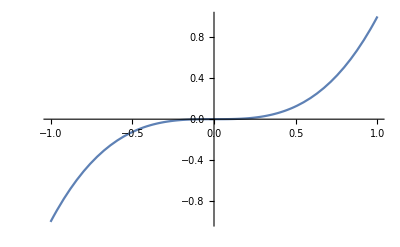

```mathematica
Plot[x^3,{x,-1,1}]
```

The plot function also supports handling more than one function; simply gather the  functions inside curly braces.

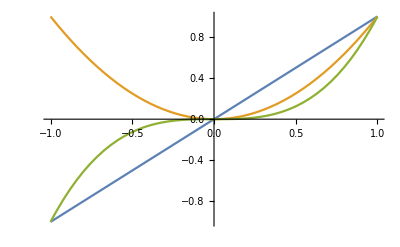

```mathematica
Plot[{x,x^2,x^3},{x,-1,1} ]
```

You can also customize graphics in color if the curve is thick or dashed; this is done with the PlotStyle option.

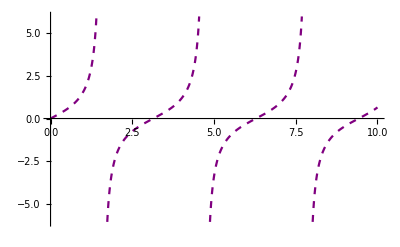

```mathematica
Plot[Tan[x],{x,0,10},PlotStyle->{Dashed,Purple}]
```

The PlotLabel option allows you to add basic descriptions to your graphics by adding a title . On the other hand, the AxesLabel option lets you add names to axes, both x and y, as depicted:

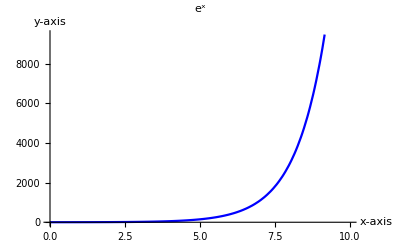

```mathematica
Plot[E^x,{x,0,10},PlotStyle->{Blue},PlotLabel->"e^x",AxesLabel->{"x-axis","y-axis"}]
```

### Logical Operators and Infix Notation

Infix notation and logical operators are commonly used in logical statements or comparisons of expressions, and the result values are either true or false .

```mathematica
{6 > 2, 3 <1, 3>=2, 4<=7, 2 == 2., 2.1 != 3, 2===2.}
```

{True,False,True,True,True,True,False}

Relational operators, also called comparison operators and logical binary operators,  check the veracity or falsity of certain relationship proposals. The expressions that  contain them are called relational expressions.

They accept various types of arguments, and the result can be true or false—that is, they are Boolean results. As you can see, they  are all binary operators, of which two are of equality condition == and !=. These serve to  verify the equality or inequality of expressions.

Boolean operands produce a true or false result or test whether a condition is  satisfied.

The AND operator returns a true value if both expressions are true. Otherwise, the  result is false.

The OR operator returns true if any of the expressions is true. Otherwise, it returns  false. This operator has an analogous operation to the previous one.

The XOR operator is an exclusive “or” operator that returns true when both  expressions differ. Otherwise, it returns false when the expressions have the same value.

The equivalent operator returns true if expressions are powered from each other.  Otherwise, it returns false.

The negation operator, also called logical negation, returns a value that can be an  expression that evaluates to a result. The result of this operator is always a Boolean type.

```mathematica
2 ==1 && 1 < 2
2==1 || 1 <2
2 ==1 ⊻ 1 <2
Power[1,2] ⧦ 1^2
¬2==1
```

False

True

True

True

«1 more identical outputs»

Another approach, instead of using Boolean operators, is to use different functions  with postfix (Q), which consists of testing whether an object meets the condition of the  built-in function. A few honorable mentions are SameQ, UnsameQ, AtomQ, IntegerQ,  and NumberQ. The next example tests whether a number is a float expression or an  integer.

```mathematica
IntegerQ[1]
IntegerQ[1.2]
```

True

False

The valuable application of the AtomQ function can tell you whether an expression  is subdivided into subexpressions. Later, you are shown how to deal with subexpressions  with lists. If the result is true, then the expression cannot be subdivided into subterms,  and if it is false, then the expression has subterms.

```mathematica
AtomQ[23]
```

True

As shown, numbers cannot be subdivided because a number is a canonic  expression; the same applies to strings, as seen before.

### Algebraic Expressions

The Wolfram Language can work with algebraic expressions. For instance, perform  symbolic computations, algebraic expansions, and simplifications. Many words used  in common language in algebra are preserved in Mathematica. To expand an algebraic  expression, use Expand.

```mathematica
Expand[(x+y+c+2 xy)^2]
```

c^2+2 c x+x^2+4 c xy+4 x xy+4 xy^2+2 c y+2 x y+4 xy y+y^2

Adding a space between variables is the same as adding the multiplication operator . This can be checked by.

```mathematica
a*x == a x
```

True

To simplify an expanded expression, use Simplify or FullSimplify.

```mathematica
Simplify[c^2+2 c x+x^2+4 c xy+4 x xy+4 xy^2+2 c y+2 x y+4 xy y+y^2]
```

(c+x+2 xy+y)^2

The difference is that the latter tries transformations to simplify the expression more  broadly. 

To unite terms over a repeated denominator, use Together. To expand into  partial fraction decomposition, use Apart.

```mathematica
Together[1/z+1/(z+4)]
```

(2 (2+z))/(z (4+z))

```mathematica
Apart[%]
```

1/z+1/(4+z)

### Solving Algebraic Equations

Various functions are accessible for finding solutions to algebraic equations. The most  common is the Solve function. The first argument is the equation or expression to be  solved, and the second is for the variable to be solved.

```mathematica
Solve[x^2 + 2 ==1, x]
```

{{x→-ⅈ},{x→ⅈ}}

as you might remember, equal is expressed as double equal ( == ); do not use one equal ( = ) because that means assigning a value to a symbol or variable.

The result means that z has two solutions: one is –1, and the other is 1. Each result is  expressed in the form of a rule. A rule expression changes the assignment of the left side  to the one on the right side (left → right) whenever it applies. 

For example, z → 1 is the  same as Rule [z, 1].  

To verify the solution, the values of z (–1, 1) must be replaced in the original  equation. For this, you can use the ReplaceAll operator (/.) along with the rule command  → or Rule, which is used to apply a transformation to a variable or a pattern with other  expressions.

```mathematica
x^2+2/.Rule[x,{ⅈ, -ⅈ}]
```

{1,1}

Multiple equations can be solved, too, given a system of equations and a list of interested variables . To solve the equations, place the system of equations in one list and the variables in another .

```mathematica
Solve[{x+y+z==2,6x-4y+5z==3,x+2y+2z==1},{x,y,z}]
```

{{x→3,y→10/9,z→-19/9}}

the results are listed. Lists are essential structures in the Wolfram Language.

The Solve function supports expressions with a mixture of logical operators, expressing y and x in terms of z .

```mathematica
Solve[x+y+z==2 &&6x-4y+5z==3,{x,y}]
```

{{x→1/10 (11-9 z),y→(9-z)/10}}

The Solve function returns the solution for each of the equations entered.  Establishing a condition with the AND operator lets you return solutions that satisfy  a condition; for example, the following equation has two solutions 1 and –1, but you can  solve the equation with the condition that z must be different from 1

```mathematica
Solve[z^-2+1==2&&z!=1,z]
```

{{z→-1}}

To obtain more general results, Reduce is used, as shown in the following example .

```mathematica
Reduce[Cos[x]==-1,x]
```

C[1]∈ℤ&&(x==-π+2 π C[1]||x==π+2 π C[1])

Here, the alternative solutions are separated by the OR operator, and the condition  is established by the AND. So this means that there are two possible solutions −π + 2πc1  or π + 2πc1 and that the constant c1 must be a number that belongs to the integers (Z). In  addition, Reduce can also solve inequalities.

```mathematica
Reduce[h^2+k2<11,{h,k}]
```

k2<11&&-√(11-k2)<h<√(11-k2)

## How Mathematica Works (Optional Reading)

## How Computations are Made

Each time Mathematica receives a computation in the input cell, it uses the  StandardForm, which is the output representation of expressions in the Wolfram  Language and has many aspects of common mathematical notation. Input can be  written in various forms, but to know how the expression is written in the Wolfram  Language, StandardForm is used.

```mathematica
StandardForm[x^2 + 1/x]
```

1/x+x^2

InputForm works similarly but produces the output acceptable to be entered as  Wolfram Language input.

```mathematica
InputForm[2+2]
InputForm[Sin[x]]
```

Sin[x]

The FullForm and TreeForm commands can be applied to view how expressions are represented symbolically. TreeForm represents the command in a graphical format,  while FullForm represents the form of the expression managed internally by the Wolfram  Language.

```mathematica
FullForm[Sin[x^2+ω/(2t)]-Cos[θ]]
```

Plus[Times[-1,Cos[\[Theta]]],Sin[Plus[Power[x,2],Times[Rational[1,2],Power[t,-1],\[Omega]]]]]

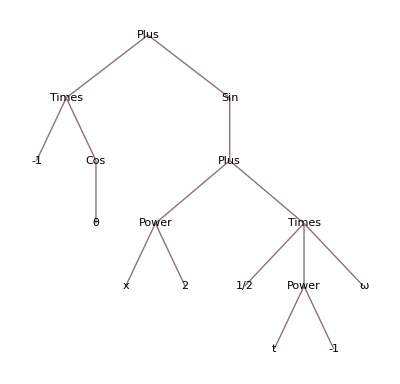

```mathematica
%//TreeForm
```

## Searching For Assistance

To learn how a function works or how built-in functions are written, the best  resource is to consult the Wolfram Documentation Center. You can also check if an  alternative input expression can be used.

So, if you need help understanding how the  Head function works, you input a question mark (?) before the function’s name, giving  you a simple understanding of how the command works

```mathematica
?Module
```

## Conclusion

This notebook served as just an introduction of the tip of the iceberg. Mathematica is a complex, and important tool in your research lifespan, and learning it would be as beneficial as understanding the calculations themselves. In a modern world, you need modern tools. Mathematica is one of them.

We’ve covered some basics of both scientific computing and Mathematica in specific. Our next lectures would jump into Quantum Mechanics itself, where our journey takes a better meaning. But I would sometimes publish notebooks under the volume 0, where we talk about some important aspects of scientific computing, data science or machine learning. Things that we might encounter during our real notebooks (volume 1-6).

If you’ve got any questions feel free to contact me both on the campus or online via my social media accounts.

Happy learning.

## Further Contents

[1] V. Ryzhov, T. Fedorova, K. Safronov, S. A. Sulaiman, and S. A. Abdul Karim, Modern Methods in Mathematical Physics: Integral Equations in Wolfram Mathematica. Singapore: Springer Nature Singapore, 2022. doi: 10.1007/978-981-19-4915-9.

[2] J. Villalobos Alva, Beginning Mathematica and Wolfram for Data Science: Applications in Data Analysis, Machine Learning, and Neural Networks. Berkeley, CA: Apress, 2024. doi: 10.1007/979-8-8688-0348-2.